```mathematica
PDF[VoigtDistribution[δ,σ],x]
```

(ⅇ^((-ⅈ x+δ)^2/(2 σ^2)) Erfc[(-ⅈ x+δ)/(√2 σ)]+ⅇ^((ⅈ x+δ)^2/(2 σ^2)) Erfc[(ⅈ x+δ)/(√2 σ)])/(2 √(2 π) σ)

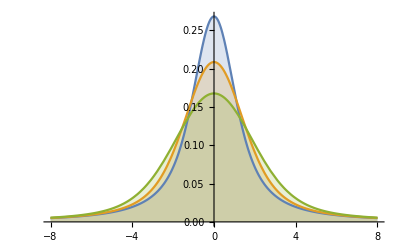

```mathematica
Plot[Table[PDF[VoigtDistribution[1,σ],x],{σ,{0.5,1.,1.5}}]//Evaluate,{x,-8,8},Exclusions->None,Filling->Axis]
```

```mathematica
skewedVoigt[μ_,δ_,σ_,skew_,x_]:=PDF[VoigtDistribution[δ,σ],(x-μ)]*(1+Erf[(skew(x-μ))/(σ √2)])
```

```mathematica
skewedVoigt[μ,δ,σ,skew,x]
```

((1+Erf[(skew (x-μ))/(√2 σ)]) (ⅇ^((-ⅈ x+δ)^2/(2 σ^2)) Erfc[(-ⅈ x+δ)/(√2 σ)]+ⅇ^((ⅈ x+δ)^2/(2 σ^2)) Erfc[(ⅈ x+δ)/(√2 σ)]))/(2 √(2 π) σ)

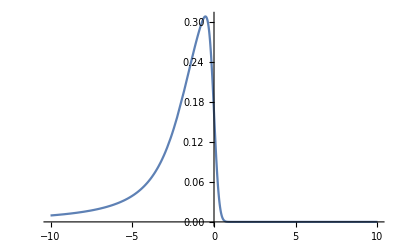

```mathematica
Plot[skewedVoigt[0,1.5,1,-4,x],{x,-10,10},PlotRange->All]
```

```mathematica
FindMaximum[skewedVoigt[0,1.5,.8,-2,x],x]
```

{0.305217,{x→-0.659493}}

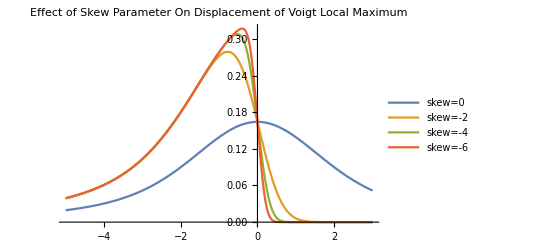

```mathematica
Plot[Table[skewedVoigt[0,1.5,1,skew,x],{skew,{0,-2,-4,-6}}]//Evaluate,{x,-5,3},PlotRange->All,PlotLegends->{"skew=0","skew=-2","skew=-4","skew=-6"},PlotLabel->"Effect of Skew Parameter On Displacement of Voigt Local Maximum"]
```

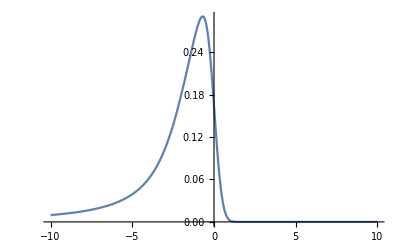

```mathematica
skewedVoigt[μ_,δ_,σ_,skew_,x_]:=PDF[VoigtDistribution[δ,σ],(x-μ)]*(1+Erf[(skew(x-μ))/(σ √2)])
Plot[skewedVoigt[0,1.5,1,-2.5,x],{x,-10,10},PlotRange->All]
```

```mathematica
NMaximize[skewedVoigt[0,1.5,1,-2.5,x],{x,-10,10}]
```

{0.290266+0. ⅈ,{x→-0.694542+0. ⅈ}}

```mathematica
μTrue=-0.6945421165370789;
```

```mathematica
𝒟=ProbabilityDistribution[skewedVoigt[0,1.5,1,-2.5,x],{x,-Infinity,Infinity}];
```

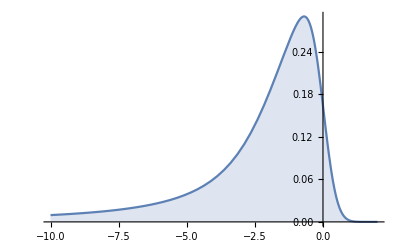

```mathematica
PDF[𝒟,x];Plot[PDF[𝒟,x],{x,-10,2},Filling->Axis]
```

```mathematica
sample=RandomVariate[𝒟[x],1]
```

RandomVariate::udist: The specification ProbabilityDistribution[((1-Erf[1.76777 x]) (ⅇ^(1/2 Plus[«2»]^2) Erfc[(1.5+Times[«2»])/(√2)]+ⅇ^(1/2 Plus[«2»]^2) Erfc[(1.5+Times[«2»])/(√2)]))/(2 √(2 π)),{x,-∞,∞}][x] is not a random distribution recognized by the system.

RandomVariate[ProbabilityDistribution[((1-Erf[1.76777 x]) (ⅇ^(1/2 (1.5-ⅈ x)^2) Erfc[(1.5-ⅈ x)/(√2)]+ⅇ^(1/2 (1.5+ⅈ x)^2) Erfc[(1.5+ⅈ x)/(√2)]))/(2 √(2 π)),{x,-∞,∞}][x],1]

```mathematica
NMaximize[skewedVoigt[0,1.5,1,-2.5,x],{x,-10,10}]
```

{0.290266+0. ⅈ,{x→-0.694542+0. ⅈ}}

```mathematica
tList=Flatten[Table[ConstantArray[x,Round[3300*skewedVoigt[0,1.5,1,-2.5,x]]],{x,-10,3,.01}]];
```

```mathematica
Histogram[tList,{.01}]
```

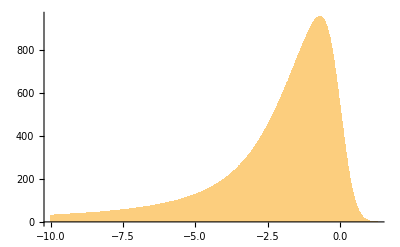

```mathematica
tSamp=RandomSample[tList,10000];
```

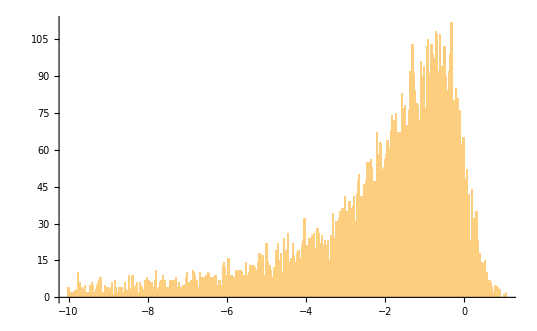

```mathematica
Histogram[tSamp,{.03}]
```

```mathematica
{xSamp,ySamp}=HistogramList[tSamp,{.03}];ySamp
```

{4,2,1,2,2,1,3,2,10,2,6,4,3,3,5,2,2,0,5,5,6,5,2,3,5,6,7,8,2,2,2,5,4,4,3,2,4,6,1,7,4,2,2,4,1,4,2,2,6,3,2,9,3,2,9,4,4,5,6,2,6,5,4,3,3,7,8,6,7,6,6,4,4,7,11,3,4,6,7,4,9,7,2,4,4,4,7,6,7,4,7,8,4,6,3,4,4,5,3,8,10,4,6,7,7,11,10,9,7,3,4,10,7,8,7,8,9,9,10,4,8,4,8,4,9,4,5,7,7,5,13,14,12,9,7,16,8,9,9,8,8,11,7,11,11,11,10,8,9,7,14,9,10,13,8,13,13,12,4,11,14,18,13,17,17,9,9,22,14,10,13,11,8,12,12,19,17,22,15,18,9,10,24,19,14,26,10,14,16,22,17,14,14,18,19,15,16,21,23,32,21,21,16,24,24,25,20,26,20,17,28,26,22,22,25,21,23,21,21,23,15,25,23,34,21,24,31,27,32,35,26,36,34,41,33,35,29,39,36,30,37,41,31,42,47,50,35,41,31,46,35,47,55,55,48,56,53,39,47,39,67,58,54,63,46,52,53,56,58,64,61,52,68,74,72,69,75,66,67,61,67,83,77,73,78,70,67,76,92,91,103,91,84,70,79,78,72,96,90,90,94,77,102,105,90,91,103,99,93,97,108,107,92,107,94,88,94,102,90,80,84,92,99,112,78,80,67,85,81,75,76,62,61,65,48,34,52,38,42,23,44,32,32,29,35,23,15,18,14,14,12,15,8,10,5,7,6,4,1,2,5,1,4,1,3,0,0,1,0,2}

```mathematica
Length[xSamp]
```

371

```mathematica
Length[ySamp]
```

370

```mathematica
Length[xSamp[[1;;-2]]]
```

370

```mathematica
xSamp[[1;;-2]];
```

```mathematica
data=Transpose[{(xSamp[[2;;]]+xSamp[[;;-2]])/2,ySamp}];
```

```mathematica
pos=Position[ySamp,Max[ySamp]][[1,1]]
xSamp[[Position[ySamp,Max[ySamp]][[1,1]]]]
```

324

-0.33

```mathematica
{xSamp[[pos]],ySamp[[pos]]}
```

{-0.33,112}

```mathematica
(*skewedVoigt[μ_,δ_,σ_,skew_,x_]*)
```

```mathematica
nlmFit=NonlinearModelFit[data,skewedVoigt[μ,δ,σ,skew,x],{{μ,0},{δ,1.5},{σ,1},{skew,-2.5}},x]
```

FittedModel[0.0109722 (1-Erf[3.29134 (-0.288706+x)]) (ⅇ^(0.00151286 (-65.6048-ⅈ x)^2) Erfc[0.0388955 (-65.6048-ⅈ x)]+ⅇ^(0.00151286 (-65.6048+ⅈ x)^2) Erfc[0.0388955 (-65.6048+ⅈ x)])]

```mathematica
nlmFit["BestFitParameters"]
```

{μ→0.288706,δ→-65.6048,σ→18.1796,skew→-84.62}

```mathematica
Nonlin
```

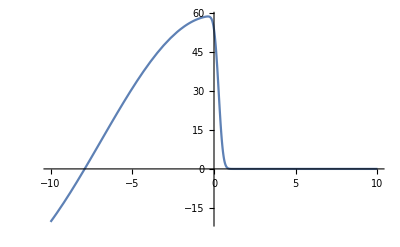

```mathematica
Plot[nlmFit[x],{x,-10,10}]
```

```mathematica
w=2;
∑_(i=-w)^w 1/(Abs[i]+1)
```

8/3

```mathematica
Table[1/(Abs[i]+1),{i,-w,w}]
```

{1/3,1/2,1,1/2,1/3}

```mathematica
t=1/(∑_(i=-w)^w 1/(Abs[i]+1))Table[1/(Abs[i]+1)*ySamp[[1+w+i;;-1-(w-i)]],{i,-w,w}];
Dimensions[t]
```

{5,366}

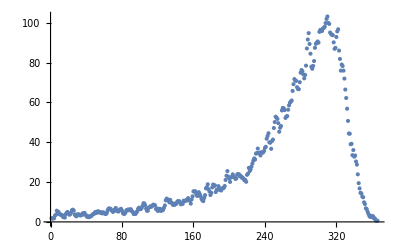

```mathematica
smoothY=∑_(i=1)^5 t[[i]];
ListPlot[smoothY]
```

```mathematica
smooth[lis_,w_]:=(t=1/(∑_(i=-w)^w 1/(Abs[i]+1))Table[1/(Abs[i]+1)*lis[[1+w+i;;-1-(w-i)]],{i,-w,w}];
smoothedLis=∑_(i=1)^(2*w+1) t[[i]])
```

```mathematica
smoothY=smooth[ySamp,2];
smoothX=smooth[(xSamp[[2;;]]+xSamp[[;;-2]])/2,2];
smoothDat=Transpose[{smoothX,smoothY}];
```

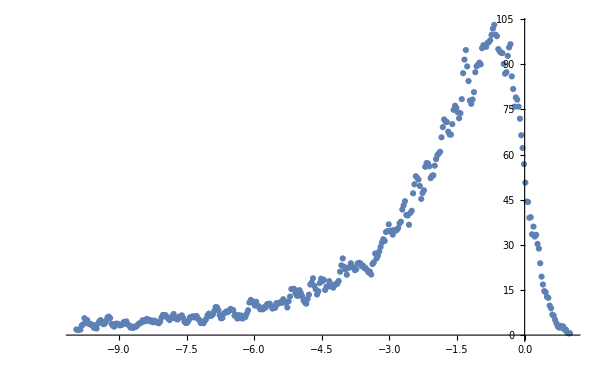

```mathematica
ListPlot[smoothDat]
```

```mathematica
nlmFit=NonlinearModelFit[smoothDat,{skewedVoigt[μ,δ,σ,skew,x],-4≤ skew≤0},{{μ,0},{δ,1.5},{σ,1},{skew,-2.5}},x]
```

$Aborted

```mathematica
smoothDat[[All,1]]
```

{-9.945,-9.915,-9.885,-9.855,-9.825,-9.795,-9.765,-9.735,-9.705,-9.675,-9.645,-9.615,-9.585,-9.555,-9.525,-9.495,-9.465,-9.435,-9.405,-9.375,-9.345,-9.315,-9.285,-9.255,-9.225,-9.195,-9.165,-9.135,-9.105,-9.075,-9.045,-9.015,-8.985,-8.955,-8.925,-8.895,-8.865,-8.835,-8.805,-8.775,-8.745,-8.715,-8.685,-8.655,-8.625,-8.595,-8.565,-8.535,-8.505,-8.475,-8.445,-8.415,-8.385,-8.355,-8.325,-8.295,-8.265,-8.235,-8.205,-8.175,-8.145,-8.115,-8.085,-8.055,-8.025,-7.995,-7.965,-7.935,-7.905,-7.875,-7.845,-7.815,-7.785,-7.755,-7.725,-7.695,-7.665,-7.635,-7.605,-7.575,-7.545,-7.515,-7.485,-7.455,-7.425,-7.395,-7.365,-7.335,-7.305,-7.275,-7.245,-7.215,-7.185,-7.155,-7.125,-7.095,-7.065,-7.035,-7.005,-6.975,-6.945,-6.915,-6.885,-6.855,-6.825,-6.795,-6.765,-6.735,-6.705,-6.675,-6.645,-6.615,-6.585,-6.555,-6.525,-6.495,-6.465,-6.435,-6.405,-6.375,-6.345,-6.315,-6.285,-6.255,-6.225,-6.195,-6.165,-6.135,-6.105,-6.075,-6.045,-6.015,-5.985,-5.955,-5.925,-5.895,-5.865,-5.835,-5.805,-5.775,-5.745,-5.715,-5.685,-5.655,-5.625,-5.595,-5.565,-5.535,-5.505,-5.475,-5.445,-5.415,-5.385,-5.355,-5.325,-5.295,-5.265,-5.235,-5.205,-5.175,-5.145,-5.115,-5.085,-5.055,-5.025,-4.995,-4.965,-4.935,-4.905,-4.875,-4.845,-4.815,-4.785,-4.755,-4.725,-4.695,-4.665,-4.635,-4.605,-4.575,-4.545,-4.515,-4.485,-4.455,-4.425,-4.395,-4.365,-4.335,-4.305,-4.275,-4.245,-4.215,-4.185,-4.155,-4.125,-4.095,-4.065,-4.035,-4.005,-3.975,-3.945,-3.915,-3.885,-3.855,-3.825,-3.795,-3.765,-3.735,-3.705,-3.675,-3.645,-3.615,-3.585,-3.555,-3.525,-3.495,-3.465,-3.435,-3.405,-3.375,-3.345,-3.315,-3.285,-3.255,-3.225,-3.195,-3.165,-3.135,-3.105,-3.075,-3.045,-3.015,-2.985,-2.955,-2.925,-2.895,-2.865,-2.835,-2.805,-2.775,-2.745,-2.715,-2.685,-2.655,-2.625,-2.595,-2.565,-2.535,-2.505,-2.475,-2.445,-2.415,-2.385,-2.355,-2.325,-2.295,-2.265,-2.235,-2.205,-2.175,-2.145,-2.115,-2.085,-2.055,-2.025,-1.995,-1.965,-1.935,-1.905,-1.875,-1.845,-1.815,-1.785,-1.755,-1.725,-1.695,-1.665,-1.635,-1.605,-1.575,-1.545,-1.515,-1.485,-1.455,-1.425,-1.395,-1.365,-1.335,-1.305,-1.275,-1.245,-1.215,-1.185,-1.155,-1.125,-1.095,-1.065,-1.035,-1.005,-0.975,-0.945,-0.915,-0.885,-0.855,-0.825,-0.795,-0.765,-0.735,-0.705,-0.675,-0.645,-0.615,-0.585,-0.555,-0.525,-0.495,-0.465,-0.435,-0.405,-0.375,-0.345,-0.315,-0.285,-0.255,-0.225,-0.195,-0.165,-0.135,-0.105,-0.075,-0.045,-0.015,0.015,0.045,0.075,0.105,0.135,0.165,0.195,0.225,0.255,0.285,0.315,0.345,0.375,0.405,0.435,0.465,0.495,0.525,0.555,0.585,0.615,0.645,0.675,0.705,0.735,0.765,0.795,0.825,0.855,0.885,0.915,0.945,0.975,1.005}

```mathematica
findXMax[dSet_]:=(xdat=dSet[[All,1]];
ydat=dSet[[All,2]];
posit=Position[ydat,Max[ydat]][[1,1]];
xdat[[posit]])
```

```mathematica
findXMax[smoothDat]
```

-0.675

```mathematica
sampleLocalMax[hList_,nSamp_,res_,smoothWidth_]:=(
rSamp=RandomSample[hList,nSamp];
{xSample,ySample}=HistogramList[rSamp,{res}];
smoothY=smooth[ySample,smoothWidth];
smoothX=smooth[(xSample[[2;;]]+xSample[[;;-2]])/2,smoothWidth];
smoothData=Transpose[{smoothX,smoothY}];
{findXMax[smoothData],smoothData})
```

-0.615

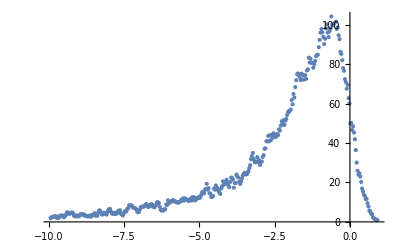

```mathematica
tSubSample=sampleLocalMax[tList,10000,0.03,2];tSubSample[[1]]
ListPlot[tSubSample[[2]]]
```

```mathematica
n=1000;
smoothSubSamples=Table[sampleLocalMax[tList,10000,0.03,2],{i,1,n}];Length[smoothSubSamples[[All,1]]]
```

1000

```mathematica
Dimensions[smoothSubSamples[[1,2]]]
```

{366,2}

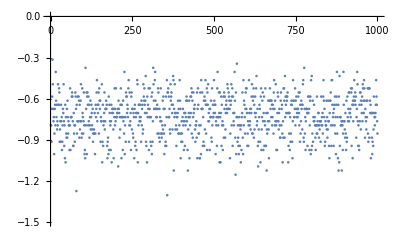

```mathematica
ListPlot[smoothSubSamples[[All,1]],PlotRange->{-1.5,0}]
```

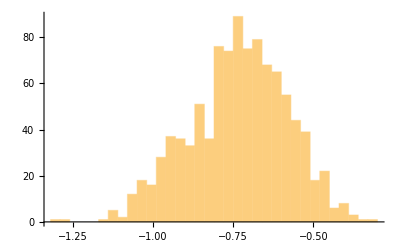

```mathematica
Histogram[smoothSubSamples[[All,1]],{.03}]
```

```mathematica
ℋ=HistogramDistribution[smoothSubSamples[[All,1]]]
```

DataDistribution[…]

```mathematica
{hLlistx,hListy}=HistogramList[smoothSubSamples[[All,1]],{.03}];
```

```mathematica
μBar=Moment[ℋ,1]
σBar=Cumulant[ℋ,2]
{p951,p952}={Quantile[ℋ,0.025],Quantile[ℋ,0.975]}
{p681,p682}={Quantile[ℋ,0.32/2],Quantile[ℋ,1-0.32/2]}
```

-0.73305

0.023641

{-1.04559,-0.4575}

{-0.898214,-0.581313}

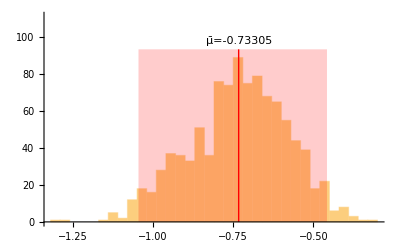

```mathematica
Histogram[smoothSubSamples[[All,1]],{.03},Epilog->{Red,Line[{{μBar,0},{μBar,Max[hlisty]*1.05}}],Black,Text["μ̄="<>ToString[μBar],{μBar,Max[hListy]*1.1}],Red,Opacity[0.2],Rectangle[{p951,0},{p952,Max[hlisty]*1.05}]},PlotRange->{0,1.25*Max[hListy]}]
```

```mathematica
ℋ["FittedDistribution"]
```

0[FittedDistribution]

```mathematica
HistogramDistribution
```

```mathematica
(μTrue-μBar)/μTrue
```

-0.0554436

```mathematica
Length[tList]
```

298421

```mathematica
SubSampleDistMaker[totalData_,nPoints_,res_,smoothingW_,n_]:=Table[sampleLocalMax[totalData,nPoints,res,smoothingW][[1]],{i,1,n}]
```

```mathematica
tSubsamps=SubSampleDistMaker[tList,10000,0.03,2,10]
```

{-0.615,-0.615,-0.825,-0.795,-0.645,-0.585,-0.585,-0.495,-0.825,-0.645}

```mathematica
nList=Table[10^i,{i,2,5}];
```

```mathematica
μCollections=Table[SubSampleDistMaker[tList,10000,0.03,2,nList[[i]]],{i,1,Length[nList]}];
```

```mathematica
xList=HistogramList[μCollections[[-1]],{.03}][[1]];
yLists=Table[1/nList[[i]] HistogramList[μCollections[[i]],{xList}][[2]],{i,1,Length[nList]}];
histLists=Table[Transpose[{(xList[[;;-2]]+xList[[2;;]])/2,yLists[[i]]}],{i,1,Length[nList]}];
```

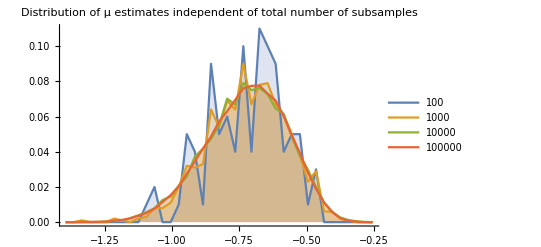

```mathematica
ListLinePlot[histLists,Filling->Axis,PlotLegends->nList,PlotLabel->"Distribution of μ estimates independent of total number of subsamples"]
```

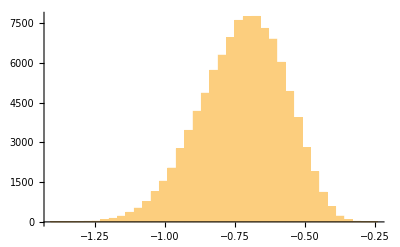

```mathematica
Histogram[μCollections[[-1]],{.03}]
```

```mathematica
ℋList=Table[HistogramDistribution[μCollections[[i]]],{i,Length[nList]}];
ℋuge=ℋList[[-1]];
```

```mathematica
μBar=Moment[ℋuge,1]
σBar=√Cumulant[ℋuge,2]
{p951,p952}={Quantile[ℋuge,0.025],Quantile[ℋuge,0.975]}
{p681,p682}={Quantile[ℋuge,0.32/2],Quantile[ℋuge,1-0.32/2]}
```

-0.724289

0.151998

{-1.04319,-0.45512}

{-0.88373,-0.574416}

0.593664 (1-Erf[5.36644 (-13284.7+x)]) (ⅇ^(4.42885 (1.938-ⅈ (-13284.7+x))^2) Erfc[2.10448 (1.938-ⅈ (-13284.7+x))]+ⅇ^(4.42885 (1.938+ⅈ (-13284.7+x))^2) Erfc[2.10448 (1.938+ⅈ (-13284.7+x))])

{0.309577+0. ⅈ,{x→13284.4+0. ⅈ}}

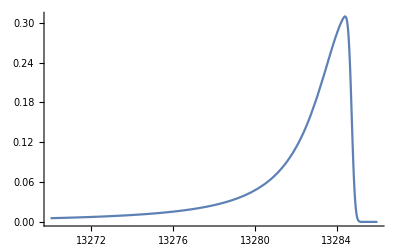

```mathematica
(*Now let's use more realistic subsample sizes*)
μ0=13284.7402;Γ0=1.938;σ0=0.336;skew0=-2.55;
f[x_]:=skewedVoigt[μ0,Γ0,σ0,skew0,x]
f[x]
NMaximize[f[x],{x,13283,13286}]
Plot[f[x],{x,13270,13286},PlotRange->All]
```

```mathematica
tList=Flatten[Table[ConstantArray[x,Round[3600*f[x]+300]],{x,13266,13286,.001}]];
Histogram[tList,{.001}]
```